```mathematica
Today
```

Day: Sat 11 Jan 2020

```mathematica
DateValue[DateObject[{2020,1,11},"Day","Gregorian",-8.],"Year"]
```

2020

```mathematica
With[{
a=FinancialData["VIXY","Price",All],
b=FinancialData["SDS","Price",All]
},
Table[
{First@First@t,Correlation[First/@Last/@t,Last/@Last/@t]},
{t,Partition[
Table[
{First@First@s,Map[Last,s]},
{s,Select[
GatherBy[
Join[
Transpose[{
a["Dates"][[;;-2]],
Map[#-1&,Ratios[a["Values"]]]
}],
Transpose[{
b["Dates"][[;;-2]],
Map[#-1&,Ratios[b["Values"]]]
}]
]
,First],
Length@#==2&]}
],10,1]}
]
]
```

{{Tue 4 Jan 2011 00:00:00GMT-8.,0.94262},{Wed 5 Jan 2011 00:00:00GMT-8.,0.947329},{Thu 6 Jan 2011 00:00:00GMT-8.,0.883594},{Fri 7 Jan 2011 00:00:00GMT-8.,0.875101},{Mon 10 Jan 2011 00:00:00GMT-8.,0.870723},{Tue 11 Jan 2011 00:00:00GMT-8.,0.872887},{Wed 12 Jan 2011 00:00:00GMT-8.,0.851248},2245,{Wed 18 Dec 2019 00:00:00GMT-8.,0.810408},{Thu 19 Dec 2019 00:00:00GMT-8.,0.807187},{Fri 20 Dec 2019 00:00:00GMT-8.,0.823127},{Mon 23 Dec 2019 00:00:00GMT-8.,0.834102},{Tue 24 Dec 2019 00:00:00GMT-8.,0.854577},{Thu 26 Dec 2019 00:00:00GMT-8.,0.854622}}
 |  |  |  |

```mathematica
FinancialData["VIXY","Name"]
```

ProShares Trust - ProShares VIX Short-Term Futures ETF

```mathematica
FinancialData["NOBL","Name"]
```

FinancialData::notent: NOBL is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Missing[NotAvailable]

```mathematica
FinancialData["^NOBL","Name"]
```

FinancialData::notent: ^NOBL is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Missing[NotAvailable]

```mathematica
FinancialData["SDS","Name"]
```

ProShares Trust - ProShares UltraShort S&P500

```mathematica
DateListPlot[
Out[7],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow"AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
DateListPlot[
Out[7],
PlotRange->{-1,1},PlotTheme->"Marketing",ColorFunction->"DarkRainbow"AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
DateListPlot[
Out[7],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[7]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
vxx=FinancialData["VIX","Price",All]
```

TimeSeries[…]

```mathematica
With[{
a=FinancialData["VIX","Price",All],
b=FinancialData["SPX","Price",All]
},
Table[
{First@First@t,Correlation[First/@Last/@t,Last/@Last/@t]},
{t,Partition[
Table[
{First@First@s,Map[Last,s]},
{s,Select[
GatherBy[
Join[
Transpose[{
a["Dates"][[;;-2]],
Map[#-1&,Ratios[a["Values"]]]
}],
Transpose[{
b["Dates"][[;;-2]],
Map[#-1&,Ratios[b["Values"]]]
}]
]
,First],
Length@#==2&]}
],10,1]}
]
]
```

{{Wed 3 Jan 1990 00:00:00GMT-8.,0.0361819},{Thu 4 Jan 1990 00:00:00GMT-8.,-0.0130243},{Fri 5 Jan 1990 00:00:00GMT-8.,-0.165989},{Mon 8 Jan 1990 00:00:00GMT-8.,-0.249966},{Tue 9 Jan 1990 00:00:00GMT-8.,-0.31267},{Wed 10 Jan 1990 00:00:00GMT-8.,-0.318248},{Thu 11 Jan 1990 00:00:00GMT-8.,-0.334531},7436,{Mon 5 Aug 2019 00:00:00GMT-8.,-0.850171},{Tue 6 Aug 2019 00:00:00GMT-8.,-0.879591},{Wed 7 Aug 2019 00:00:00GMT-8.,-0.88036},{Thu 8 Aug 2019 00:00:00GMT-8.,-0.881621},{Fri 9 Aug 2019 00:00:00GMT-8.,-0.902152},{Mon 12 Aug 2019 00:00:00GMT-8.,-0.887179}}
 |  |  |  |

```mathematica
DateListPlot[
Out[17],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Last/@Out[17],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Total[Last/@Out[17]]/Length[Last/@Out[17]]
```

-0.366767

```mathematica
data=Last/@Out[17];
```

```mathematica
Mean@data
```

-0.366767

```mathematica
Median@data
```

-0.429435

```mathematica
Quartiles@data
```

{-0.648895,-0.429435,-0.133069}

```mathematica
GeometricMean@data
```

0.331216+0.00013969 ⅈ

```mathematica
DiscreteWaveletTransform[data]
```

DiscreteWaveletData[<<DWT>>, <13>, {7449}]

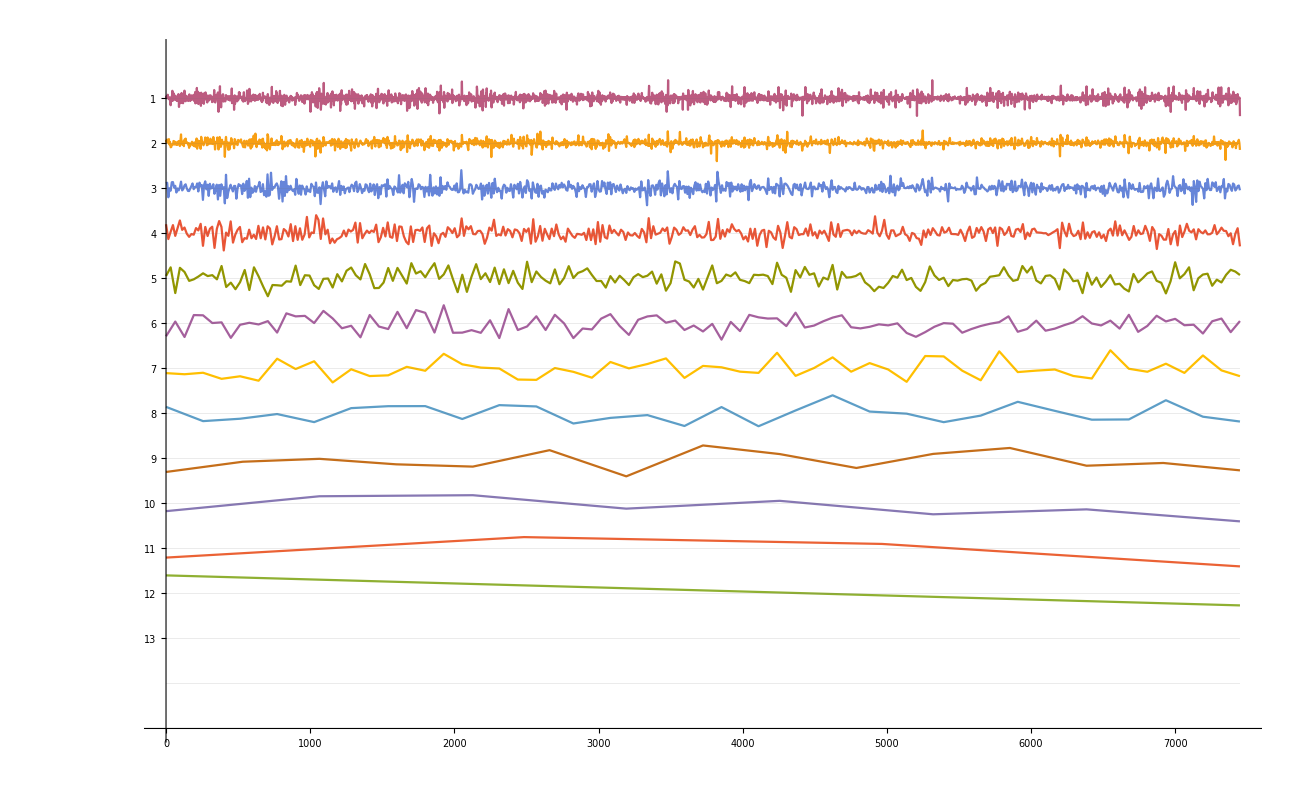

```mathematica
WaveletListPlot[%26]
```

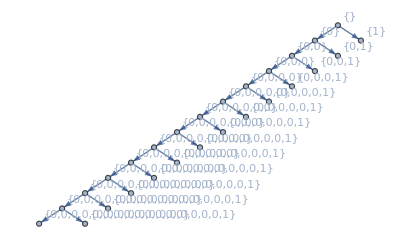

```mathematica
%26["TreeView"]
```

```mathematica
WaveletScalogram[%26]
```

-Graphics-